# SUGRA Base Classification (det-sq-nons)

## All bases from det-sq-nons/

## Setup

```mathematica
SetDirectory["~/Desktop/sugra_pipeline"];
Get["SUGRACatalog`"];
```

SUGRACatalog loaded.

entries = LoadCatalog["cat_1ext"]

CatalogSummary[entries]

ShowEntry[entries[[1]]]  (* copy-pasteable IF *)

FindEntries[entries, "e8"]

TMin[entry], TMax[entry]

## Define Classification Functions

```mathematica
nhcToGauge = <|
  "-3" -> "su3",
  "-4" -> "so8",
  "-5" -> "f4",
  "-6" -> "e6",
  "-7" -> "e7'",
  "-8" -> "e7",
  "-12" -> "e8",
  "-2-3" -> "su2+g2",
  "-2-4" -> "su2+so16",
  "-2-3-2" -> "su2+so7+su2",
  "-2-2-3" -> "sp1+g2",
  "pure-2" -> "",
  "???" -> "???"
|>;
nhcGaugeName[nhcName_String] := Lookup[nhcToGauge, nhcName, nhcName];

LSTGauge[entry_Association] := Module[
  {IF = entry["IF"], n, extIdxs, nonM1, visited, gauges = {}},
  n = Length[IF];
  extIdxs = ExtIndices[entry] + 1;
  nonM1 = Select[Range[n], IF[[#, #]] != -1 && !MemberQ[extIdxs, #] &];
  visited = Association[Thread[nonM1 -> False]];
  Do[
    If[!visited[s],
      Module[{comp = {}, queue = {s}},
        visited[s] = True;
        While[Length[queue] > 0,
          Module[{cur = First[queue]},
            queue = Rest[queue];
            AppendTo[comp, cur];
            Do[If[!visited[nb] && IF[[cur, nb]] != 0,
              visited[nb] = True; AppendTo[queue, nb]], {nb, nonM1}]]];
        comp = Sort[comp];
        Module[{subIF, nhcResult, gName},
          subIF = IF[[comp, comp]];
          nhcResult = NHCLookup[subIF];
          gName = nhcGaugeName[nhcResult["name"]];
          If[gName =!= "" && gName =!= Null,
            AppendTo[gauges, gName]]]]],
    {s, nonM1}];
  If[gauges === {}, "(none)",
    StringRiffle[Sort[gauges], " + "]]
];

ExtGauge[entry_Association] := Module[
  {exts = entry["externals"], gauges},
  gauges = Table[
    Switch[ext["extSI"],
      -2, "su2", -3, "su3", -4, "so8", -5, "f4",
      -6, "e6", -7, "e7'", -8, "e7", -12, "e8", -1, "hat1",
      _, ToString[ext["extSI"]]],
    {ext, exts}];
  StringRiffle[Sort[gauges], "+"]
];
```

## Load all catalogs from det-sq-nons/

```mathematica
base = "det-sq-nons/";
dirs = Select[FileNames["cat_*", base], DirectoryQ];
Print["Found ", Length[dirs], " catalog directories"];
```

Found 60 catalog directories

```mathematica
allDSQ = Join @@ (LoadCatalog /@ dirs);
Print["Total entries: ", Length[allDSQ]];
```

Loaded 0 entries from det-sq-nons/cat_10ext_t010

Loaded 16247 entries from det-sq-nons/cat_1ext_t010

Loaded 31 entries from det-sq-nons/cat_1ext_t101110

Loaded 24 entries from det-sq-nons/cat_1ext_t111120

Loaded 29952 entries from det-sq-nons/cat_1ext_t1120

Loaded 17 entries from det-sq-nons/cat_1ext_t121130

Loaded 0 entries from det-sq-nons/cat_1ext_t131140

Loaded 17711 entries from det-sq-nons/cat_1ext_t2130

Loaded 8560 entries from det-sq-nons/cat_1ext_t3140

Loaded 4526 entries from det-sq-nons/cat_1ext_t4150

Loaded 2755 entries from det-sq-nons/cat_1ext_t5160

Loaded 947 entries from det-sq-nons/cat_1ext_t6170

Loaded 364 entries from det-sq-nons/cat_1ext_t7180

Loaded 152 entries from det-sq-nons/cat_1ext_t8190

Loaded 82 entries from det-sq-nons/cat_1ext_t91100

Loaded 25822 entries from det-sq-nons/cat_2ext_t010

Loaded 0 entries from det-sq-nons/cat_2ext_t101110

Loaded 0 entries from det-sq-nons/cat_2ext_t111120

Loaded 24139 entries from det-sq-nons/cat_2ext_t1120

Loaded 0 entries from det-sq-nons/cat_2ext_t121130

Loaded 10662 entries from det-sq-nons/cat_2ext_t2130

Loaded 3690 entries from det-sq-nons/cat_2ext_t3140

Loaded 1823 entries from det-sq-nons/cat_2ext_t4150

Loaded 483 entries from det-sq-nons/cat_2ext_t5160

Loaded 66 entries from det-sq-nons/cat_2ext_t6170

Loaded 11 entries from det-sq-nons/cat_2ext_t7180

Loaded 4 entries from det-sq-nons/cat_2ext_t8190

Loaded 3 entries from det-sq-nons/cat_2ext_t91100

Loaded 37425 entries from det-sq-nons/cat_3ext_t010

Loaded 7011 entries from det-sq-nons/cat_3ext_t1120

Loaded 1373 entries from det-sq-nons/cat_3ext_t2130

Loaded 248 entries from det-sq-nons/cat_3ext_t3140

Loaded 87 entries from det-sq-nons/cat_3ext_t4150

Loaded 4 entries from det-sq-nons/cat_3ext_t5160

Loaded 0 entries from det-sq-nons/cat_3ext_t6170

Loaded 0 entries from det-sq-nons/cat_3ext_t7180

Loaded 0 entries from det-sq-nons/cat_3ext_t8190

Loaded 0 entries from det-sq-nons/cat_3ext_t91100

Loaded 29598 entries from det-sq-nons/cat_4ext_t010

Loaded 1322 entries from det-sq-nons/cat_4ext_t1120

Loaded 77 entries from det-sq-nons/cat_4ext_t2130

Loaded 19 entries from det-sq-nons/cat_4ext_t3140

Loaded 3 entries from det-sq-nons/cat_4ext_t4150

Loaded 6635 entries from det-sq-nons/cat_5ext_t010

Loaded 33 entries from det-sq-nons/cat_5ext_t1120

Loaded 0 entries from det-sq-nons/cat_5ext_t2130

Loaded 319 entries from det-sq-nons/cat_6ext_t010

Loaded 2 entries from det-sq-nons/cat_6ext_t1120

Loaded 40 entries from det-sq-nons/cat_7ext_t010

Loaded 0 entries from det-sq-nons/cat_7ext_t1120

Loaded 28 entries from det-sq-nons/cat_8ext_t010

Loaded 7 entries from det-sq-nons/cat_9ext_t010

Loaded 2131 entries from det-sq-nons/cat_nhc_ext

Loaded 1536 entries from det-sq-nons/cat_nhc_ext_2ext

Loaded 1750 entries from det-sq-nons/cat_nhc_ext_3ext

Loaded 1161 entries from det-sq-nons/cat_nhc_ext_4ext

Loaded 269 entries from det-sq-nons/cat_nhc_ext_5ext

Loaded 25 entries from det-sq-nons/cat_nhc_ext_6ext

Loaded 1 entries from det-sq-nons/cat_nhc_ext_7ext

Loaded 0 entries from det-sq-nons/cat_nhc_ext_8ext

Total entries: 239175

## Entry Count by directory

```mathematica
counts = Table[
  Module[{d = FileNameTake[dir, -1], entries = LoadCatalog[dir]},
    {d, Length[entries]}],
  {dir, dirs}];
Grid[Prepend[SortBy[counts, First],
  {Style["Directory", Bold], Style["Count", Bold]}],
  Frame -> All]
```

Loaded 0 entries from det-sq-nons/cat_10ext_t010

Loaded 16247 entries from det-sq-nons/cat_1ext_t010

Loaded 31 entries from det-sq-nons/cat_1ext_t101110

Loaded 24 entries from det-sq-nons/cat_1ext_t111120

Loaded 29952 entries from det-sq-nons/cat_1ext_t1120

Loaded 17 entries from det-sq-nons/cat_1ext_t121130

Loaded 0 entries from det-sq-nons/cat_1ext_t131140

Loaded 17711 entries from det-sq-nons/cat_1ext_t2130

Loaded 8560 entries from det-sq-nons/cat_1ext_t3140

Loaded 4526 entries from det-sq-nons/cat_1ext_t4150

Loaded 2755 entries from det-sq-nons/cat_1ext_t5160

Loaded 947 entries from det-sq-nons/cat_1ext_t6170

Loaded 364 entries from det-sq-nons/cat_1ext_t7180

Loaded 152 entries from det-sq-nons/cat_1ext_t8190

Loaded 82 entries from det-sq-nons/cat_1ext_t91100

Loaded 25822 entries from det-sq-nons/cat_2ext_t010

Loaded 0 entries from det-sq-nons/cat_2ext_t101110

Loaded 0 entries from det-sq-nons/cat_2ext_t111120

Loaded 24139 entries from det-sq-nons/cat_2ext_t1120

Loaded 0 entries from det-sq-nons/cat_2ext_t121130

Loaded 10662 entries from det-sq-nons/cat_2ext_t2130

Loaded 3690 entries from det-sq-nons/cat_2ext_t3140

Loaded 1823 entries from det-sq-nons/cat_2ext_t4150

Loaded 483 entries from det-sq-nons/cat_2ext_t5160

Loaded 66 entries from det-sq-nons/cat_2ext_t6170

Loaded 11 entries from det-sq-nons/cat_2ext_t7180

Loaded 4 entries from det-sq-nons/cat_2ext_t8190

Loaded 3 entries from det-sq-nons/cat_2ext_t91100

Loaded 37425 entries from det-sq-nons/cat_3ext_t010

Loaded 7011 entries from det-sq-nons/cat_3ext_t1120

Loaded 1373 entries from det-sq-nons/cat_3ext_t2130

Loaded 248 entries from det-sq-nons/cat_3ext_t3140

Loaded 87 entries from det-sq-nons/cat_3ext_t4150

Loaded 4 entries from det-sq-nons/cat_3ext_t5160

Loaded 0 entries from det-sq-nons/cat_3ext_t6170

Loaded 0 entries from det-sq-nons/cat_3ext_t7180

Loaded 0 entries from det-sq-nons/cat_3ext_t8190

Loaded 0 entries from det-sq-nons/cat_3ext_t91100

Loaded 29598 entries from det-sq-nons/cat_4ext_t010

Loaded 1322 entries from det-sq-nons/cat_4ext_t1120

Loaded 77 entries from det-sq-nons/cat_4ext_t2130

Loaded 19 entries from det-sq-nons/cat_4ext_t3140

Loaded 3 entries from det-sq-nons/cat_4ext_t4150

Loaded 6635 entries from det-sq-nons/cat_5ext_t010

Loaded 33 entries from det-sq-nons/cat_5ext_t1120

Loaded 0 entries from det-sq-nons/cat_5ext_t2130

Loaded 319 entries from det-sq-nons/cat_6ext_t010

Loaded 2 entries from det-sq-nons/cat_6ext_t1120

Loaded 40 entries from det-sq-nons/cat_7ext_t010

Loaded 0 entries from det-sq-nons/cat_7ext_t1120

Loaded 28 entries from det-sq-nons/cat_8ext_t010

Loaded 7 entries from det-sq-nons/cat_9ext_t010

Loaded 2131 entries from det-sq-nons/cat_nhc_ext

Loaded 1536 entries from det-sq-nons/cat_nhc_ext_2ext

Loaded 1750 entries from det-sq-nons/cat_nhc_ext_3ext

Loaded 1161 entries from det-sq-nons/cat_nhc_ext_4ext

Loaded 269 entries from det-sq-nons/cat_nhc_ext_5ext

Loaded 25 entries from det-sq-nons/cat_nhc_ext_6ext

Loaded 1 entries from det-sq-nons/cat_nhc_ext_7ext

Loaded 0 entries from det-sq-nons/cat_nhc_ext_8ext

Directory | Count
cat_10ext_t010 | 0
cat_1ext_t010 | 16247
cat_1ext_t101110 | 31
cat_1ext_t111120 | 24
cat_1ext_t1120 | 29952
cat_1ext_t121130 | 17
cat_1ext_t131140 | 0
cat_1ext_t2130 | 17711
cat_1ext_t3140 | 8560
cat_1ext_t4150 | 4526
cat_1ext_t5160 | 2755
cat_1ext_t6170 | 947
cat_1ext_t7180 | 364
cat_1ext_t8190 | 152
cat_1ext_t91100 | 82
cat_2ext_t010 | 25822
cat_2ext_t101110 | 0
cat_2ext_t111120 | 0
cat_2ext_t1120 | 24139
cat_2ext_t121130 | 0
cat_2ext_t2130 | 10662
cat_2ext_t3140 | 3690
cat_2ext_t4150 | 1823
cat_2ext_t5160 | 483
cat_2ext_t6170 | 66
cat_2ext_t7180 | 11
cat_2ext_t8190 | 4
cat_2ext_t91100 | 3
cat_3ext_t010 | 37425
cat_3ext_t1120 | 7011
cat_3ext_t2130 | 1373
cat_3ext_t3140 | 248
cat_3ext_t4150 | 87
cat_3ext_t5160 | 4
cat_3ext_t6170 | 0
cat_3ext_t7180 | 0
cat_3ext_t8190 | 0
cat_3ext_t91100 | 0
cat_4ext_t010 | 29598
cat_4ext_t1120 | 1322
cat_4ext_t2130 | 77
cat_4ext_t3140 | 19
cat_4ext_t4150 | 3
cat_5ext_t010 | 6635
cat_5ext_t1120 | 33
cat_5ext_t2130 | 0
cat_6ext_t010 | 319
cat_6ext_t1120 | 2
cat_7ext_t010 | 40
cat_7ext_t1120 | 0
cat_8ext_t010 | 28
cat_9ext_t010 | 7
cat_nhc_ext | 2131
cat_nhc_ext_2ext | 1536
cat_nhc_ext_3ext | 1750
cat_nhc_ext_4ext | 1161
cat_nhc_ext_5ext | 269
cat_nhc_ext_6ext | 25
cat_nhc_ext_7ext | 1
cat_nhc_ext_8ext | 0

## Compute Classification

```mathematica
classData = Monitor[
  Table[With[{e = allDSQ[[i]]},
    <|"T" -> e["baseT"],
      "extGauge" -> ExtGauge[e],
      "lstGauge" -> LSTGauge[e],
      "Tsugra" -> e["T"],
      "det" -> e["det"],
      "uni" -> (Abs[e["det"]] == 1),
      "extCount" -> Length[e["externals"]]|>],
    {i, Length[allDSQ]}],
  ProgressIndicator[i, {1, Length[allDSQ]}]
];
```

### Classification Table

```mathematica
groups = GroupBy[classData, {#["T"], #["extGauge"], #["lstGauge"]} &];
classTable = SortBy[
  KeyValueMap[
    <|"T_LST" -> #1[[1]], "External" -> #1[[2]],
      "LST_Gauge" -> #1[[3]], "Count" -> Length[#2],
      "T_range" -> MinMax[#2[[All, "Tsugra"]]]|> &,
    groups],
  {#["T_LST"], -#["Count"]} &
];
```

```mathematica
Dataset[classTable[[;; Min[50, Length[classTable]]]]]
```

### Summary by T_LST

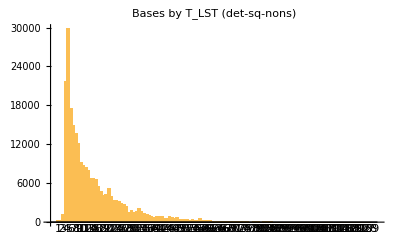

```mathematica
tSummary = SortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["T"] &]],
  First];
BarChart[tSummary[[All, 2]], ChartLabels -> tSummary[[All, 1]],
  PlotLabel -> "Bases by T_LST (det-sq-nons)"]
```

### Summary by External Gauge

```mathematica
extSummary = ReverseSortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["extGauge"] &]],
  Last];
Grid[Prepend[extSummary,
  {Style["External", Bold], Style["Count", Bold]}],
  Frame -> All]
```

External | Count
su2 | 54361
su2+su2 | 36899
su2+su2+su2 | 36845
su2+su2+su2+su2 | 28742
su3 | 11173
su2+su3 | 10048
su2+su2+su2+su2+su2 | 6340
su2+su2+su3 | 5014
so8 | 4182
f4 | 3839
su3+su3 | 3057
e6 | 2865
so8+su2 | 2496
e7 | 2132
su2+su2+su2+su3 | 2060
so8+su3 | 1931
f4+su2 | 1906
e7' | 1873
f4+su3 | 1541
su2+su3+su3 | 1481
so8+su2+su2 | 1327
e6+su2 | 1151
e6+su3 | 1044
e8 | 919
su2+su2+su2+su2+su3 | 830
su2+su2+su3+su3 | 784
f4+so8 | 781
so8+so8 | 619
e7'+su2 | 599
e7+su2 | 588
e7+su3 | 569
e7'+su3 | 566
e6+f4 | 553
e6+so8 | 521
su2+su2+su2+su3+su3 | 496
so8+su2+su3 | 490
f4+f4 | 477
so8+su2+su2+su2 | 462
su3+su3+su3 | 316
e7+f4 | 315
e7'+f4 | 315
f4+su2+su2 | 313
e6+e6 | 299
e7+so8 | 289
e7'+so8 | 287
su2+su2+su2+su2+su2+su2 | 286
e6+e7' | 278
e6+e7 | 278
so8+su2+su2+su3 | 277
f4+su2+su3 | 248
e7+e7' | 205
su2+su2+su2+su2+su3+su3 | 201
su2+su2+su2+su2+su2+su3 | 177
e7+e7 | 167
e6+su2+su2 | 167
e6+su2+su3 | 144
e7'+e7' | 141
e8+su3 | 134
e8+su2 | 118
so8+so8+su2 | 109
su2+su3+su3+su3 | 103
f4+so8+su2 | 99
so8+su2+su2+su2+su2 | 95
so8+su2+su2+su2+su3 | 90
so8+su3+su3 | 87
e8+f4 | 83
e6+e8 | 81
f4+f4+su2 | 79
e7+e8 | 77
e8+so8 | 71
e7+su2+su2 | 71
e7'+su2+su2 | 71
e7'+su2+su3 | 70
e7+su2+su3 | 68
e6+so8+su2 | 66
e7'+e8 | 64
e6+f4+su2 | 61
so8+su2+su3+su3 | 56
e8+e8 | 51
f4+su2+su2+su2 | 50
e6+e6+su2 | 40
su2+su2+su2+su2+su2+su2+su2 | 36
f4+su3+su3 | 36
e7+so8+su2 | 35
so8+so8+su2+su2 | 34
e7'+so8+su2 | 34
e7'+f4+su2 | 31
so8+su2+su2+su2+su2+su3 | 30
e7+f4+su2 | 30
su2+su2+su2+su2+su2+su3+su3 | 24
su2+su2+su2+su2+su2+su2+su2+su2 | 24
hat1 | 24
f4+su2+su2+su3 | 24
hat1+su2 | 23
e6+e7'+su2 | 22
so8+so8+so8 | 21
e6+su2+su2+su2 | 21
e6+e7+su2 | 21
su3+su3+su3+su3 | 18
so8+su3+su3+su3 | 17
so8+so8+su3 | 17
su2+su2+su2+su2+su2+su2+su3 | 15
so8+su2+su2+su3+su3 | 13
e6+e6+su3 | 13
e7+e7'+su2 | 12
e6+su3+su3 | 12
f4+f4+su2+su2 | 11
e6+f4+su3 | 11
su2+su2+su3+su3+su3 | 10
e7+e7+su2 | 10
e7'+e7'+su2 | 10
so8+su2+su2+su2+su2+su2 | 9
so8+so8+su2+su2+su2 | 9
f4+su2+su2+su2+su2 | 9
f4+so8+su2+su2 | 9
e6+su2+su2+su3 | 9
hat1+su2+su2 | 8
f4+su2+su3+su3 | 8
e8+su2+su3 | 8
e7+su2+su2+su2 | 8
e7'+su2+su2+su2 | 8
e7+f4+su3 | 7
e6+so8+su3 | 7
e6+f4+su2+su3 | 7
f4+f4+su3 | 6
e8+su2+su2 | 6
e7+so8+su3 | 6
e7'+f4+su3 | 6
e6+so8+su2+su3 | 6
e6+e7'+su3 | 6
e6+e6+su2+su3 | 6
so8+su2+su3+su3+su3 | 5
so8+so8+su2+su3 | 5
f4+su3+su3+su3 | 5
f4+so8+su3 | 5
f4+so8+so8 | 5
f4+f4+f4 | 5
e7'+so8+su3 | 5
e6+so8+so8 | 5
e6+f4+su2+su2 | 5
su2+su2+su2+su2+su2+su2+su2+su3 | 4
su2+su2+su2+su2+su2+su2+su2+su2+su2 | 4
so8+su2+su2+su2+su3+su3 | 4
hat1+su3 | 4
f4+f4+su2+su3 | 4
f4+f4+so8 | 4
e8+so8+su2 | 4
e8+f4+su2 | 4
e7+su3+su3 | 4
e7'+su3+su3 | 4
e6+hat1+su2 | 4
e6+e7+su3 | 4
su2+su2+su2+su3+su3+su3 | 3
so8+so8+so8+su2 | 3
so8+so8+so8+so8 | 3
f4+so8+su2+su3 | 3
e8+su3+su3 | 3
e8+so8+su3 | 3
e8+f4+su3 | 3
e7+so8+su2+su3 | 3
e7'+so8+su2+su3 | 3
e7+hat1+su3 | 3
e7+f4+su2+su3 | 3
e7'+f4+su2+su3 | 3
e7'+e8+su2 | 3
e6+su2+su3+su3 | 3
e6+so8+su2+su2 | 3
e6+so8+so8+su2 | 3
e6+hat1 | 3
e6+f4+so8 | 3
e6+e8+su2 | 3
e6+e6+so8 | 3
su2+su2+su2+su2+su2+su2+su2+su2+su3 | 2
hat1+so8+so8+su2 | 2
hat1+so8+so8 | 2
f4+su2+su3+su3+su3 | 2
f4+so8+so8+su2 | 2
f4+hat1+su2 | 2
f4+hat1 | 2
f4+f4+f4+su2 | 2
e7+su2+su3+su3 | 2
e7'+su2+su3+su3 | 2
e7+so8+so8 | 2
e7'+hat1+su3 | 2
e7+f4+so8 | 2
e7'+f4+so8 | 2
e7+e8+su2 | 2
e6+su2+su2+su2+su2 | 2
e6+hat1+su3 | 2
e6+hat1+su2+su3 | 2
e6+f4+so8+su2 | 2
e6+f4+f4 | 2
e6+e6+so8+su2 | 2
su2+su3+su3+su3+su3 | 1
so8+su2+su2+su2+su2+su2+su2+su2+su2 | 1
so8+su2+su2+su2+su2+su2+su2+su2 | 1
so8+su2+su2+su2+su2+su2+su2 | 1
so8+so8+su3+su3+su3 | 1
so8+so8+su2+su2+su3 | 1
so8+so8+su2+su2+su2+su2 | 1
so8+so8+so8+su2+su2 | 1
hat1+su3+su3+su3 | 1
hat1+su2+su3+su3+su3 | 1
hat1+so8+su2 | 1
hat1+so8 | 1
hat1+hat1+su2 | 1
f4+su2+su2+su3+su3 | 1
f4+su2+su2+su2+su2+su2 | 1
f4+f4+su2+su2+su2 | 1
f4+f4+so8+su2 | 1
f4+f4+hat1 | 1
e8+hat1+su3 | 1
e7'+so8+so8 | 1
e7+hat1+su2+su3 | 1
e7'+hat1+su2+su3 | 1
e7+hat1+so8 | 1
e7+e7+su3 | 1
e7+e7'+su3 | 1
e7'+e7'+su3 | 1
e7'+e7'+so8 | 1
e6+so8+so8+su3 | 1
e6+e7'+su2+su3 | 1
e6+e7+so8 | 1
e6+e7'+so8 | 1
e6+e6+su3+su3 | 1
e6+e6+su2+su2 | 1
e6+e6+f4 | 1
e6+e6+e6 | 1

### Summary by LST Gauge (top 30)

```mathematica
lstSummary = ReverseSortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["lstGauge"] &]],
  Last];
Grid[Prepend[lstSummary[[;; Min[30, Length[lstSummary]]]],
  {Style["LST Gauge", Bold], Style["Count", Bold]}],
  Frame -> All]
```

LST Gauge | Count
su2+g2 + su3 | 20774
su3 + su3 | 10528
su2+g2 + su2+g2 | 6716
su2+so7+su2 + su3 | 6504
so8 | 4698
f4 + su3 + su3 + su3 | 4620
f4 | 4125
so8 + su2+g2 + su3 | 3426
f4 + su2+g2 + su3 + su3 | 3132
so8 + so8 | 3092
e6 + f4 + su3 | 3041
so8 + so8 + so8 | 2312
e6 + e6 + f4 + su3 + su3 | 2096
e6 | 2011
e6 + e6 + e6 + su3 + su3 | 2008
e6 + f4 + su2+g2 | 1460
su2+g2 | 1432
sp1+g2 + su2+g2 | 1419
su2+g2 + su2+so7+su2 | 1368
so8 + su2+g2 + su2+g2 | 1364
so8 + so8 + so8 + so8 | 1359
sp1+g2 + su3 | 1344
(none) | 1241
e6 + e6 + e6 + f4 + su3 + su3 + su3 | 1200
f4 + su3 | 1170
f4 + su3 + su3 | 1074
e6 + e6 + su2+so7+su2 | 993
f4 + su2+g2 + su3 | 991
e7 + su2+g2 + su2+g2 + su2+so7+su2 | 985
su2+so7+su2 | 971

## Unimodular vs Non-unimodular

```mathematica
uniCount = Count[classData, _?(#["uni"] &)];
nonuniCount = Length[classData] - uniCount;
PieChart[{uniCount, nonuniCount},
  ChartLabels -> {"Uni (" <> ToString[uniCount] <> ")",
    "Non-uni (" <> ToString[nonuniCount] <> ")"},
  PlotLabel -> "det distribution"]
```

-Graphics-

## Summary by ext count

```mathematica
extCountSummary = SortBy[
  KeyValueMap[{#1, Length[#2]} &, GroupBy[classData, #["extCount"] &]],
  First];
Grid[Prepend[extCountSummary,
  {Style["# Externals", Bold], Style["Count", Bold]}],
  Frame -> All]
```

# Externals | Count
1 | 81368
2 | 68632
3 | 47650
4 | 32793
5 | 7908
6 | 712
7 | 76
8 | 29
9 | 7

## Export to CSV

```mathematica
Export["classification_detsq.csv",
  Prepend[
    Table[{c["T_LST"], c["External"], c["LST_Gauge"], c["Count"]},
      {c, classTable}],
    {"T_LST", "External", "LST_Gauge", "Count"}]];
Print["Exported to classification_non_detsq.csv"]
```

Exported to classification_non_detsq.csv